## 导入数据

```mathematica
SetDirectory[NotebookDirectory[]];
csvdir="..\\csv_data\\"
data10=Reverse[Drop[Import[csvdir<>"008087.csv"],1]ᵀ[[3]]ᵀ];
data1=Table[{i,data10[[i]]},{i,-Length[data10],-1}];
datadate1=Drop[Import[csvdir<>"008087.csv"],1]ᵀ[[2]];
data20=Reverse[Drop[Import[csvdir<>"008299.csv"],1]ᵀ[[3]]ᵀ];
data2=Table[{i,data20[[i]]},{i,-Length[data20],-1}];
datadate2=Drop[Import[csvdir<>"008299.csv"],1]ᵀ[[2]];
```

..\csv_data\

## 计算日期的天数差

```mathematica
DaysDifference[date1_String,date2_String]:=Module[{dateObj1,dateObj2,daysDifference},

(*将字符串转换为日期对象*)dateObj1=DateObject[
{ToExpression[StringTake[date1,{1,4}]],ToExpression[StringTake[date1,{6,7}]],ToExpression[StringTake[date1,{9,10}]]}];

dateObj2=DateObject[{ToExpression[StringTake[date2,{1,4}]],ToExpression[StringTake[date2,{6,7}]],ToExpression[StringTake[date2,{9,10}]]}];

(*计算天数差*)
daysDifference=AbsoluteTime[dateObj2]-AbsoluteTime[dateObj1];

(*返回天数差*)
daysDifference/86400  (*将秒转换为天*)
]
actualdatadate[datadate_]:=Reverse[Table[DaysDifference[datadate[[1]],datadate[[i]]]-1,{i,1,Length@datadate}]]
```

## 计算平均趋势线

### 函数拟合算法（拟合函数（参数不多不少，不过拟合）；拟合窗口；是否对近期数据加权？；曲线修正）

```mathematica
averageHistoryFit[data_,function_]:=
Module[{fitfunc},
fitfunc=FindFit[data,function[[1]]@x,function[[2]],x];
(function[[1]]/.fitfunc)
]
```

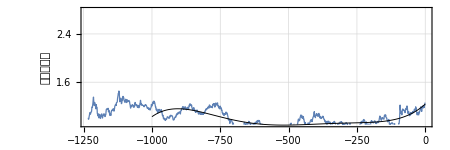

```mathematica
fitfunc1=averageHistoryFit[data1[[-1000;;-1]],{{a #^2+b #+c+d #^3+e #^4+ f #^5}&,{a,b,c,d,e,f}}][x];
Show[
ListLinePlot[data1,AspectRatio->1/3,PlotStyle->{PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.9,2.8}},FrameLabel->{"交易日（天）","净值（元）"}
],
Plot[{fitfunc1[[1]]},{x,-1000,0},PlotStyle->{Black,Thickness[0.0015]},PlotPoints->200],ImageSize->450
]
```

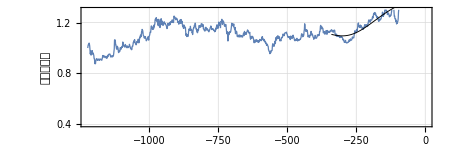

```mathematica
fitfunc2=averageHistoryFit[data2[[-400;;-1]],{{a #^2+b #+c+d #^3+e #^4+ f #^5}&,{a,b,c,d,e,f}}][x];
Show[
ListLinePlot[data2,AspectRatio->1/3,PlotStyle->{PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.4,1.3}},FrameLabel->{"交易日（天）","净值（元）"}
],
Plot[{fitfunc2[[1]]},{x,-340,0},PlotStyle->{Black,Thickness[0.0015]}],ImageSize->450
]
```

## 时间序列预测 holt-winter

```mathematica
HoltRollingPredict[data_,α_,β_]:=Module[{times,values,n,levels,trends,forecasts,predSteps=1},{times,values}=Transpose[data];
n=Length[times];
levels=ConstantArray[0.,n];
trends=ConstantArray[0.,n];
forecasts=ConstantArray[0.,n];
levels[[1]]=values[[1]];
trends[[1]]=If[n>1,values[[2]]-values[[1]],0];
Do[If[i>1,levels[[i]]=α*values[[i]]+(1-α)*(levels[[i-1]]+trends[[i-1]]);
trends[[i]]=β*(levels[[i]]-levels[[i-1]])+(1-β)*trends[[i-1]]];
If[i<n,forecasts[[i+1]]=levels[[i]]+trends[[i]]*predSteps],{i,1,n}
];
Transpose[{times,forecasts}]
];
```

### 计算举例+可视化

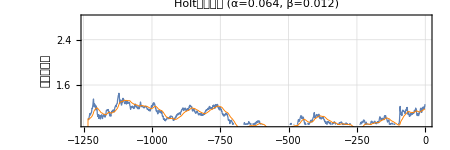

```mathematica
(*手动调节参数*)
alpha=0.064;  (*水平平滑因子，建议范围0.1-0.5*)
beta=0.012;   (*趋势平滑因子，建议范围0.05-0.3*)
result=HoltRollingPredict[data1,alpha,beta];
Show[
ListLinePlot[data1,AspectRatio->1/3,PlotStyle->{PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.9,2.8}},FrameLabel->{"交易日（天）","净值（元）"},PlotLabel->Style[StringForm["Holt预测分析 (α=``, β=``)",alpha,beta],12]
],
ListLinePlot[result,PlotStyle->{Orange,Thickness[0.0015]}],ImageSize->450
]
```

### 涨落天数可视化

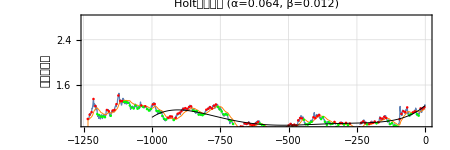

```mathematica
datapart=7;
pointred=Cases[{data1ᵀ[[1]],(data1-result)ᵀ[[2]]}ᵀ[[;;;;datapart]],u_/;u[[2]]>0]ᵀ[[1]];
pointgreen=Cases[{data1ᵀ[[1]],(data1-result)ᵀ[[2]]}ᵀ[[;;;;datapart]],u_/;u[[2]]<0]ᵀ[[1]];
Show[
ListLinePlot[data1,AspectRatio->1/3,PlotStyle->{PointSize[0.1],Thickness[0.002]},
PlotTheme->"Detailed",PlotRange->{Full,{0.9,2.8}},FrameLabel->{"交易日（天）","净值（元）"},PlotLabel->Style[StringForm["Holt预测分析 (α=``, β=``)",alpha,beta],12]
],
ListLinePlot[result,PlotStyle->{Orange,Thickness[0.0015]}],

ListPlot[{data1[[pointred]],data1[[pointgreen]]},AspectRatio->1/3,PlotStyle->{{Red,PointSize[0.004]},{Green,PointSize[0.004]}}],
Plot[{fitfunc1[[1]]},{x,-1000,0},PlotStyle->{Black,Thickness[0.0015]},PlotPoints->200],
ImageSize->450
]
```

## 购买策略——总资产计算模型

输入：	1. 基金1历史价值，如{{-234, 1.0},{-233,1.32},{-232,1.25},...,{-1,1.34}}，-1代表前1天，-233代表前233天，第二项代表基金单价
		2. 基金2历史价值，数据形式如1
		3. 购买策略，如{{-233,0.2,-0.3},{-32,0.1,0.2},...}，代表在-233天花费资金0.2购入了基金1，卖出了资金0.3量的基金2，0代表不操作
输出：	{时间（从第一次开始操作算起），总资产，基金1价值（基金1数量*当前单价），基金2价值（基金2数量*当前单价），资金开支（-1代表总共花费1现金，0.3代表手头赚了0.3现金）}

### 包含手续费的计算模型

```mathematica
CalculateInvestmentResultwithCommission[fund1History_,fund2History_,strategy_]:=
Module[{
(*申购费率+赎回费率*)commissionrate=(0.5)*0.01,
fund1money,fund2money,fundresult,fundresultall
},
fundresult=Table[
fund1money=Total[Table[If[strategy[[j,2]]>0,1-commissionrate,1]*(*买入由于手续费，需要折损*)
strategy[[j,2]]/fund1History[[strategy[[j,1]],2]],{j,1,i}]]*fund1History[[strategy[[i,1]],2]];
fund2money=Total[Table[If[strategy[[j,3]]>0,1-commissionrate,1]*(*买入由于手续费，需要折损*)
strategy[[j,3]]/fund2History[[strategy[[j,1]],2]],{j,1,i}]]*fund2History[[strategy[[i,1]],2]];

{strategy[[i,1]],
fund1money+fund2money-Total[Flatten[Table[strategy[[j,{2,3}]],{j,1,i}]]],
fund1money,
fund2money,
-Total[Flatten[Table[strategy[[j,{2,3}]],{j,1,i}]]]
}
,{i,1,Length@strategy}]
]
```

## 购买策略指定函数

输入：	1.  基金1历史价值，如 {{-234, 1.0}, {-233, 1.32}, {-232, 1.25}, ..., {-1, 1.34}}，-1 代表前1天，-233 代表前233天，第二项代表基金单价
		2.  基金2历史价值，数据形式如1
输出：	 购买策略，如 {{-233, 0.2, -0.3}, {-32, 0.1, 0.2}, ...}，代表在 - 233 天花费资金0 .2 购入了基金1，卖出了资金0 .3 量的基金2，0 代表不操作

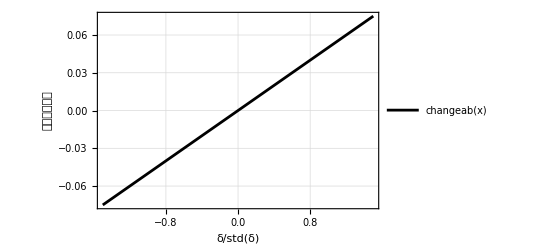

```mathematica
changeab[flucstd_]:=0.05flucstd
Plot[changeab[x],{x,-1.5,1.5},
ExclusionsStyle->Dashed,PlotTheme->"Detailed",GridLines->Automatic,
PlotStyle->Black,Axes->True,FrameLabel->{"δ/std(δ)","操作持仓比例"}]
```

### 策略2(加入真实时间)——双基金+初始(beginday)全仓买入+周期性(changeperoid)调仓（A比例为ratioA，B比例ratioB，均线估计alpha12/beta12，调仓函数为changeab[]）

```mathematica
strategy2[data1_,data2_,α1_,β1_,α2_,β2_,beginday_,ratioA_,ratioB_,datadate1_,datadate2_]:=
Module[{changeperoid=7,predictdatadate1,predictdatadate2,flucdata1,flucdata2,deltafluc,deltaflucstd,operateall,operateperiod,adatadate1,adatadate2,realbeginday1,realbeginday2,daybd1,daybd2,fromday,buyday,buyposition},
(*计算预测平均数据*)
predictdatadate1=HoltRollingPredict[data1,α1,β1];
predictdatadate2=HoltRollingPredict[data2,α2,β2];

(*计算平均值附近的涨落数据*)
flucdata1={data1ᵀ[[1]],data1ᵀ[[2]]-predictdatadate1ᵀ[[2]]}ᵀ;
flucdata2={data2ᵀ[[1]],data2ᵀ[[2]]-predictdatadate2ᵀ[[2]]}ᵀ;

(*根据datadate生成历史自然时间差*)
adatadate1=actualdatadate[datadate1];
adatadate2=actualdatadate[datadate2];
(*找到符合条件的realbeginday12，可能beginday不是交易日，则取下一个日期*)
realbeginday1=Min[Cases[adatadate1-beginday,u_/;u>=0]]+beginday;
realbeginday2=Min[Cases[adatadate2-beginday,u_/;u>=0]]+beginday;
(*找到这两天位于（第前几个交易日）*)
daybd1=data1[[Flatten[Position[adatadate1,realbeginday1]],1]][[1]];
daybd2=data2[[Flatten[Position[adatadate2,realbeginday2]],1]][[1]];

(*判断从daybd1开始，按照周期changeperoid，可以进行交易的项目（时间间隔大于等于changeperiod）*)
fromday=daybd1;
buyday=Table[If[data1[[i,1]]<daybd1,False,
If[adatadate1[[i]]-adatadate1[[fromday]]<changeperoid,False,fromday=data1[[i,1]];True]
]
,{i,1,Length@adatadate1}];
(*购买点位于交易日的位置buyposition*)
buyposition=Flatten[Position[buyday,True]];
(*倒数*)
buyposition=buyposition-Length@data1-1;

(*计算涨落数据的差值，1-2，差值大于0意味着要卖1，买2*)
deltafluc={flucdata1[[buyposition[[1]];;-1,1]],flucdata1[[buyposition[[1]];;-1,2]]-flucdata2[[buyposition[[1]];;-1,2]]}ᵀ;
deltaflucstd=StandardDeviation[deltaflucᵀ[[2]]];
(*计算操作量，生成全时间操作函数，卖出代表负值*)
operateall={deltaflucᵀ[[1]],-changeab/@(deltaflucᵀ[[2]]/deltaflucstd),changeab/@(deltaflucᵀ[[2]]/deltaflucstd)}ᵀ;

(*根据changeperoid删减生成新的操作函数*)
operateperiod=Table[operateall[[i]],{i,buyposition}];

(*加入初始买入ratioA和ratioB*)
operateperiod[[1,2]]=operateperiod[[1,2]]+ratioA;
operateperiod[[1,3]]=operateperiod[[1,3]]+ratioA;

(*操作后一天的值只能*)
DeleteCases[{operateperiodᵀ[[1]]+1,operateperiodᵀ[[2]],operateperiodᵀ[[3]]}ᵀ,u_/;u[[1]]==0]
(*
(*填补上每日的操作，包含0操作*)
DeleteCases[operateperiod,u_/;u[[2]]==0];*)
]
```

### 可视化（红点卖出，绿点买入）

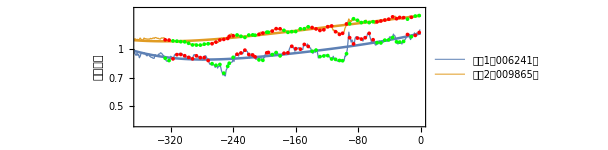

```mathematica
resstra=strategy2[data1,data2,0.018000000000000002,0.054,0.018000000000000002,0.054,-500,0.5,0.5,datadate1,datadate2];
resstra0=Flatten[{{{-323,0.5,0.5}},Table[{i,0,0},{i,-322,-1}]},1];
fitfunc1=averageHistoryFit[data1[[-400;;-1]],{{a #^2+b #+c+d #^3+e #^4}&,{a,b,c,d,e}}][x];
fitfunc2=averageHistoryFit[data2[[-400;;-1]],{{a #^2+b #+c+d #^3+e #^4}&,{a,b,c,d,e}}][x];
resstraApoint=Cases[resstra,u_/;u[[2]]>0]ᵀ[[1]];
resstraBpoint=Cases[resstra,u_/;u[[2]]<0]ᵀ[[1]];
Show[
ListLinePlot[{data1,data2},AspectRatio->1/3,PlotStyle->Directive[Thickness[0.002]],PlotTheme->"Detailed",AspectRatio->1/3,FrameLabel->{"交易日（天）","基金净值"},PlotRange->{{-360,-1},{0.4,1.6}},ImageSize->450,PlotLegends->{"基金1（006241）","基金2（009865）"},ScalingFunctions->{None,"Log"}],
LogPlot[{fitfunc1[[1]],fitfunc2[[1]]},{x,-400,0},PlotStyle->{Thickness[0.004]}],

ListLogPlot[{data1[[resstraApoint]],data1[[resstraBpoint]]},PlotStyle->{{PointSize[0.006],Green},{PointSize[0.006],Red}}],
ListLogPlot[{data2[[resstraApoint]],data2[[resstraBpoint]]},PlotStyle->{{PointSize[0.006],Red},{PointSize[0.006],Green}}]
]
```

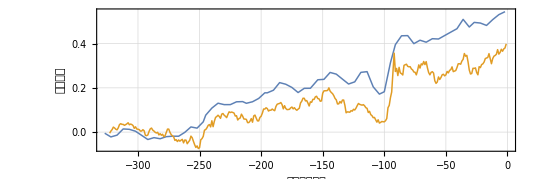

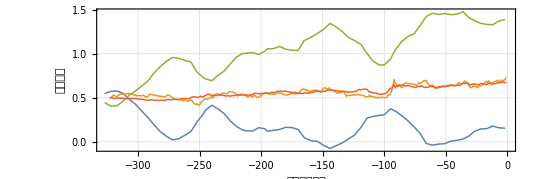

```mathematica
res1=CalculateInvestmentResultwithCommission[data1,data2,resstra];
res2=CalculateInvestmentResultwithCommission[data1,data2,resstra0];
ListLinePlot[{res1[[;;,{1,2}]],res2[[;;,{1,2}]]},PlotStyle->{{PointSize[0.1],Thickness[0.002]},{PointSize[0.1],Thickness[0.002]}},
PlotTheme->"Detailed",AspectRatio->1/3,FrameLabel->{"交易日（天）","总盈利率"},PlotRange->Full]
ListLinePlot[{res1[[;;,{1,3}]],res2[[;;,{1,3}]],res1[[;;,{1,4}]],res2[[;;,{1,4}]]},PlotStyle->{{PointSize[0.1],Thickness[0.002]},{PointSize[0.1],Thickness[0.002]}},
PlotTheme->"Detailed",AspectRatio->1/3,FrameLabel->{"交易日（天）","总盈利率"},PlotRange->Full]
```

## 参数优化

优化HoltWinter模型的alpha，beta值

假设短操作周期changeperoid，连续不间断的操作函数changeab，和合理的操作幅值

固定股票、操作起始点

对于α1,β1打点

对于α2,β2打点

对于α1,β1打点......循环优化

对于短操作周期，优化操作函数changeab

给定操作周期，继续优化changeab

优化初始仓分配ratioA, ratioB

### 结果发现，操作幅值越大越容易爆仓，a,b越小越容易爆仓，周期越短越容易爆仓

因此固定周期T=7天，固定函数；
在不爆仓的前提下：同时优化a，b，操作幅值A。

优化初始仓分配ratioA, ratioB

#### 参数打点计算

```mathematica
resultabA=Table[
changeab[flucstd_]:=A flucstd;
{A,Table[resstra=strategy2[data1,data2,α1,β1,α1,β1,-500,0.5,0.5,datadate1,datadate2];
result1=CalculateInvestmentResultwithCommission[data1,data2,resstra];
If[Length[Cases[Flatten[result1ᵀ[[{3,4}]]],u_/;u<0.01]]>0(*爆仓检验*),{α1,β1,Null},{α1,β1,result1[[-1,2]]}],
{α1,0.01,0.2,0.02},{β1,0.008,0.15,0.02}
]},{A,0.01,0.2,0.02}];
```

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]]
Save["resultabA.txt",resultabA]
```

C:\Users\Rick\Desktop\FundModel_rick\FundPair_0225\6_008087_008299

#### 分析优化结果

```mathematica
SetDirectory[NotebookDirectory[]];
Get["resultabA.txt"];
```

```mathematica
ListPointPlot3D[Cases[Flatten[resultabA[[3]][[2]],1],u_/;RealValuedNumberQ[u[[3]]]==True],PlotRange->Full]
```

-Graphics3D-

```mathematica
maxpara=DeleteCases[#,u_/;Length[u[[2]]]==0]&@Table[{resultabA[[j,1]],MaximalBy[DeleteCases[Flatten[resultabA[[j,2]],1],u_/;u[[3]]==Null],Last]},{j,1,Length@resultabA}];
shiftmaxpara={#[[1]],Mean[#[[2]]]}&/@maxpara;
```

```mathematica
ListPlot[shiftmaxpara[[;;,2,{1,2}]],PlotTheme->"Scientific",FrameLabel->{"α","β"},ColorFunction->"DarkRainbow",PlotRange->Full]
```

-Graphics-

```mathematica
ListPointPlot3D[shiftmaxpara[[;;,2]],PlotTheme->"Scientific",(*FrameLabel->{"α","β","3"},*)ColorFunction->"DarkRainbow",PlotRange->Full]
```

-Graphics3D-

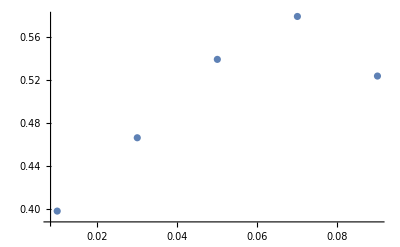

```mathematica
ListPlot[{shiftmaxparaᵀ[[1]],shiftmaxparaᵀ[[2,;;,3]]}ᵀ,PlotRange->Full]
```

#### 最优收益模型——无操作模型可视化对比

```mathematica
shiftmaxpara[[4]]
```

{0.07,{0.07,0.008,0.578602}}

```mathematica
num1=4;
changeab[flucstd_]:=shiftmaxpara[[num1,1]] flucstd;
resstra1=strategy2[data1,data2,shiftmaxpara[[num1,2,1]],shiftmaxpara[[num1,2,2]],shiftmaxpara[[num1,2,1]],shiftmaxpara[[num1,2,2]],-395,0.5,0.5,datadate1,datadate2];
res1=CalculateInvestmentResultwithCommission[data1,data2,resstra1];
num0=1;
changeab[flucstd_]:=0 flucstd;
resstra0=strategy2[data1,data2,shiftmaxpara[[num0,2,1]],shiftmaxpara[[num0,2,2]],shiftmaxpara[[num0,2,1]],shiftmaxpara[[num0,2,2]],-395,0.5,0.5,datadate1,datadate2];
res0=CalculateInvestmentResultwithCommission[data1,data2,resstra0];
```

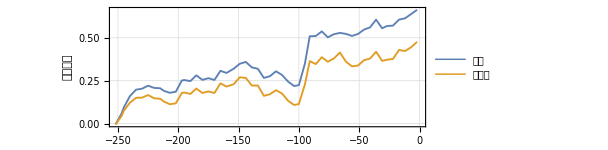

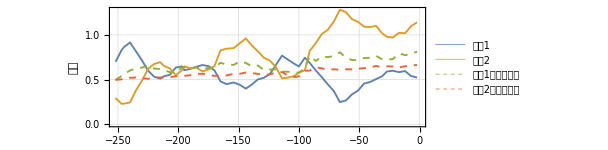

```mathematica
ListLinePlot[{res1[[;;,{1,2}]],res0[[;;,{1,2}]]},PlotStyle->{{PointSize[0.1],Thickness[0.003]},{PointSize[0.1],Thickness[0.003]}},
PlotTheme->"Detailed",AspectRatio->1/3,FrameLabel->{"交易日（天）","总盈利率"},PlotRange->Full,ImageSize->450,PlotLegends->{"策略","无操作"},Axes->True]
ListLinePlot[{res1[[;;,{1,3}]],res1[[;;,{1,4}]],res0[[;;,{1,3}]],res0[[;;,{1,4}]]},PlotStyle->{{PointSize[0.1],Thickness[0.003]},{PointSize[0.1],Thickness[0.003]},{PointSize[0.1],Thickness[0.003],Dashed},{PointSize[0.1],Thickness[0.003],Dashed}},
PlotTheme->"Detailed",AspectRatio->1/3,FrameLabel->{"交易日（天）","份额"},PlotRange->Full,PlotLegends->{"基金1","基金2","基金1（无操作）","基金2（无操作）"},ImageSize->450]
```